```mathematica
(*defaultContext = $ContextPath;
$ContextPath = defaultContext;  Prepend[defaultContext, "lliosadefcalculus`"];*)
$Context = "lliosadefcalculus`";
```

## DPS equation

```mathematica
multipliers = {hp/(66/25), 1/(100/(100+(ar/20))) }
ehp = Times@@multipliers
Plot3D[ehp, {hp,0,5000}, {ar,0,5000}]
```

{(25 hp)/66,1/100 (100+ar/20)}

1/264 (100+ar/20) hp

-Graphics3D-

```mathematica
constraints = {hp ≥ 0, ar ≥ 0, hp + ar == 10000};
{knownBestEHP,knownBestDistro} = Maximize[{ehp,constraints}, {hp,ar}]
```

{75000/11,{hp→6000,ar→4000}}

## Path of steepest ascent

```mathematica
g = Grad[ehp /. {hp -> x, ar -> y}, {x,y}]
```

{1/264 (100+y/20),x/5280}

```mathematica
{{hp2arUnbounded}} = {y[x]} /. DSolve[{
	y'[x] == (g[[1]] /. y -> y[x]) / (g[[2]] /. y -> y[x]), 
	y[hp /. knownBestDistro] == (ar /. knownBestDistro)}, 
	{y[x]}, x]

hp2ar[attack_] := Max[0,hp2arUnbounded] /. x -> attack
```

{{-2000+x}}

```mathematica
gHPodd = x /. Solve[{hp2ar[x] + Max[0,x] == h, h ≥ 0}, x, 
					Method -> Reduce]
gHPfixed = Piecewise[gHPodd /. ConditionalExpression[xx_, yy_] :> {xx, yy}]

gHP[gold_] := gHPfixed /. h -> gold
gAR[h_] := hp2ar[gHP[h]]
gDistroDef[h_] := {gHP[h],gAR[h]}
```

{ConditionalExpression[h,0<h<2000],ConditionalExpression[(2000+h)/2,h>2000]}

Piecewise[{{h, 0<h<2000}, {(2000+h)/2, h>2000}, {0, True}}]

15000

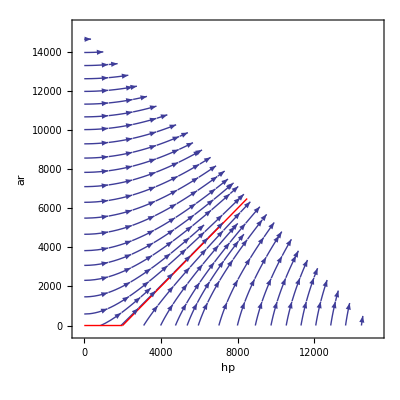

-Graphics3D-

```mathematica
graphLimit = 15000
Show[
  StreamPlot[g, {x, 0, graphLimit}, {y, 0, graphLimit}, 
	RegionFunction -> Function[{x, y, z}, x + y < graphLimit],
	AxesLabel -> {hp,ar}], 

  ParametricPlot[{gHP[u], gAR[u]}, {u, 0, graphLimit}, 
	PlotStyle -> Directive[Red, Thick]]
]

Show[
	Plot3D[ehp, {hp,0,graphLimit}, {ar,0,graphLimit}, 
	ColorFunction -> Function[{x, y, z},  ColorData["Thermometer"][z]], 
	AxesLabel-> Automatic,
    RegionFunction -> Function[{x, y, z}, x + y < graphLimit]
],

  ParametricPlot3D[{gHP[u], gAR[u], ehp /. {hp -> gHP[u], ar -> gAR[u]}}, {u, 0, graphLimit}, 
	PlotStyle -> Directive[Red, Thickness[0.01]]]
]
```

```mathematica
Clear[scale,gDistroDefScale]
ehp2 = (hp/(66/25))/(100/(100+(ar/20))scale + (1 - scale))
hmm = gDistroDef[h] //. {2000 -> v, -2000 -> -v}
gDistroDefScale[a_,b_] := hmm /. {h -> a, v -> b}
gDistroDefScale[u,Infinity]
FullSimplify@PiecewiseExpand@gDistroDefScale[u,v]
f = With[{x=gDistroDefScale[u,Piecewise[{{2000/scale,scale>0}},Infinity]]}, Flatten@{x, ehp2 /. {hp -> x⟦1⟧, ar -> x⟦2⟧}}]
```

(25 hp)/(66 (1-scale+(100 scale)/(100+ar/20)))

{Piecewise[{{h, 0<h<v}, {(h+v)/2, h>v}, {0, True}}],Max[0,-v+(Piecewise[{{h, 0<h<v}, {(h+v)/2, h>v}, {0, True}}])]}

{Piecewise[{{u, 0<u<∞}, {∞, u>∞}, {0, True}}],Max[0,-∞+(Piecewise[{{u, 0<u<∞}, {∞, u>∞}, {0, True}}])]}

Piecewise[{{{u,0}, u<v&&u>0}, {{(u+v)/2,(u-v)/2}, u>v}, {{0,0}, (v≥0&&(u==v||(u≤0&&u≤v)))||(u<v&&u>0)}, {{0,-v}, True}}]

{Piecewise[{{u, 0<u<(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {1/2 (u+(Piecewise[{{2000/scale, scale>0}, {∞, True}}])), u>(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {0, True}}],Max[0,-(Piecewise[{{2000/scale, scale>0}, {∞, True}}])+(Piecewise[{{u, 0<u<(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {1/2 (u+(Piecewise[{{2000/scale, scale>0}, {∞, True}}])), u>(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {0, True}}])],(25 (Piecewise[{{u, 0<u<(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {1/2 (u+(Piecewise[{{2000/scale, scale>0}, {∞, True}}])), u>(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {0, True}}]))/(66 (1-scale+(100 scale)/(100+1/20 Max[0,-(Piecewise[{{2000/scale, scale>0}, {∞, True}}])+(Piecewise[{{u, 0<u<(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {1/2 (u+(Piecewise[{{2000/scale, scale>0}, {∞, True}}])), u>(Piecewise[{{2000/scale, scale>0}, {∞, True}}])}, {0, True}}])])))}

```mathematica
slices = Map[	
Show[Plot3D[ehp2 /. scale -> #, {hp,0,graphLimit}, {ar,0,graphLimit}, 
	ColorFunctionScaling -> False,
	ColorFunction -> Function[{x, y, z},  ColorData["Thermometer"][Rescale[z,{0,graphLimit},{0,1}]]], 
	AxesLabel-> {"Health (gold)","Armor (gold)","Effective-HP"}, 
	Mesh -> None,  ClippingStyle -> Black,
	PlotStyle -> Directive[Green, Opacity[0.4], Specularity[White, 20]],
    RegionFunction -> Function[{x, y, z}, x + y < graphLimit]],
ParametricPlot3D[f /. scale -> #, {u, 0, graphLimit},  
		PlotStyle -> Directive[Purple, Thickness[0.002], Opacity[1]]
		]
]&, {4/4,3/4,2/4,1/4,0}];

Show[slices, 
	ParametricPlot3D[f /. scale -> v, {u, 0, graphLimit}, {v,0,1}, 
		PlotStyle -> Directive[Purple, Thickness[0.05], Opacity[0.8]],
		(*Mesh -> 10, MeshFunctions -> {#3 &},*) Mesh -> None,
		BoundaryStyle -> None],
	Boxed -> False,
	PlotRange -> {0,15000}
]

	ParametricPlot3D[f /. scale -> v, {u, 0, graphLimit}, {v,0,1}, 
		PlotStyle -> Directive[Purple, Thickness[0.05], Opacity[0.8]],
		(*Mesh -> 10, MeshFunctions -> {#3 &},*) Mesh -> None,
		BoundaryStyle -> None, PlotRange -> {0,15000}]
```

-Graphics3D-

-Graphics3D-